# Quantum Fourier Transform

Definitionpaclet:Q3/tutorial/QuantumFourierTransform#1875748448 | Quantum Implementationpaclet:Q3/tutorial/QuantumFourierTransform#727891409
Physical Meaningpaclet:Q3/tutorial/QuantumFourierTransform#1970601676 | Semiclassical Implementationpaclet:Q3/tutorial/QuantumFourierTransform#1845626348

See also Section 4.3 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

The quantum Fourier transform is a unitary transformation of quantum states. It is analogous to the discrete Fourier transform of a finite set of numbers. In the case of the quantum Fourier transform, the numbers are replaced with quantum states.

The quantum Fourier transform can be performed efficiently on a quantum computer consisting of n qubits with only O(n^2) elementary quantum gate operations, compared to O(n 2^n) gates for the best known classical algorithm for a discrete Fourier transform. This exponential speedup in the quantum Fourier transform algorithm relative to the classical counterpart enabled the celebrated quantum factorization algorithm to achieve a similar efficiency.

Apart from the above mentioned quantum factorization algorithm, the quantum Fourier transformation is a key part of many other quantum algorithms, such as the quantum phase estimation, the order-finding problem, the discrete logarithm, and most importantly the hidden subgroup problem. Such a wide range of applications of the quantum Fourier transform stems from the fact that all known quantum algorithms featuring an exponential speedup over classical algorithms are variations of the hidden subgroup problem and, as first realized by Kitaev (1996), the key step to solve the latter problem is the quantum Fourier transform.

QFTpaclet:Q3/ref/QFTQ3 Package Symbol | Represents the quantum Fourier transform
ControlledPowerpaclet:Q3/ref/ControlledPowerQ3 Package Symbol | Represents a controlled-power of unitary operator
ControlledGatepaclet:Q3/ref/ControlledGateQ3 Package Symbol | Represents a controlled-unitary gate

Q3 functions related to the quantum Fourier transform.

Make sure that the Q3 framework is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

## Definition

To make the physical meaning underlying the quantum Fourier transform clearer, in this document, we use a slightly different notation for the computational basis states, and denote them by

X_x:=x_1⊗x_2⊗⋯⊗x_n

for x=0,1,2,…,2^n-1, where x_k for k=1,2,…,n are the binary digits of x=(x_1 x_2(⋯x)_n)_2.

The quantum Fourier transform, QFT for short, is a unitary transformation defined by the association

U_QFT X_y:=1/2^(n/2)Σ_(x=0)^(2^n-1)X_x ⅇ^(ⅈ x p_y)

for y=0,1,2,…,2^n-1, where p_y is the y^th “wave number” defined by

p_y:=(2π y)/2^n=2(π(0. y_1 y_2(⋯y)_n))_2.

Like x_k, y_k for k=1,2,…,n are the binary digits of y=(y_1 y_2(⋯y)_n)_2.

The expression on the right-hand side of the above definition is of a familiar form of the discrete Fourier transform except that instead of numerical coefficients for the exponential factor ⅇ^(ⅈ x p_y), there appear state vectors. Therefore, one may think of the quantum Fourier transform as a vector-valued discrete Fourier transformation.

## Physical Meaning

In many physical applications, there is a more important aspect of the quantum Fourier transform than its formal similarity to the discrete Fourier transform. It is useful and inspiring to regard the QFT as a basis change, a unitary transformation from the computational basis

{X_x:x=0,1,2,…,2^n-1}

to the so-called “conjugate basis”

{P_y:=U_QFT X_y:y=0,1,2,…,2^n-1}.

The key observation is that in the “continuum” limit (L := 2^n→ ∞), the computational basis corresponds to the eigenbasis of the “position” and the conjugate basis to that of the “momentum”. Indeed, one can see that the two observables

X:=Σ_x X_xxX_x     and     P:=Σ_y P_y p_y P_y

bearing eigenvalues x and p_y, respectively, satisfy the relation

ⅇ^(-ⅈ a P)X ⅇ^(+ⅈ a P)=X - a I.

This implies that ⅇ^(-ⅈ a P)is a translation operator, and P is the generator of the translation, i.e., the momentum.

This notion can be made rigorous even in a finite-dimensional Hilbert space using the unitary operators exp(-ⅈ p X) and exp(-ⅈ a P), which generate the so-called Weyl-Heisenberg group;  see Weyl (1931, Section IV.14) for example.

The quantum Fourier transform appears frequently in many quantum algorithms (notably the quantum phase estimation algorithm), in an explicit or disguised form. The relation between the computational and conjugate basis defined above is useful to understand the principle behind the particular algorithms.

## Quantum Implementation

The quantum Fourier transform algorithm is to efficiently implement the unitary operator U_QFT in terms of the elementary gates. Getting back to the definition, the quantum Fourier transform maps the quantum states by

U_QFT X_y:=1/2^(n/2)Σ_(x=0)^(2^n-1)X_x ⅇ^(ⅈ x p_y)

with wave number

p_y:=(2π y)/2^n

for y=0,1,2,…,2^n-1.

Since the characteristic properties of the Fourier transform of any kind are attributed to an oscillatory phase factor ⅇ^(ⅈ x p_y), we start by elaborating it. The product x p_y in the exponent is given by

x p_y=(2π x y)/2^n=2(π(0. x_1 x_2(⋯x)_n))_2 y=2π yΣ_(k=1)^n x_k 2^-k,

which recasts the phase factor into the form

exp(ⅈ x p_y)=Π_(k=1)^n exp(2π ⅈ y x_k 2^-k).

We put it back in the defining expression of quantum Fourier transform in the above, and rewrite the sum over x with the sum over bit values x_k∈{0,1}, which lead to

U_QFT X_y=⊗_(k=1)^n Σ_(x_k=0,1)x_k ⅇ^(2π ⅈ x_k y/2^k).

For a fixed k, the ratio y/2^k is represented in binary digits as

y/2^k=(y_1 y_2(⋯y)_(n-k).y_(n-k+1)(⋯y)_(n-1)y_n)_2.

The integer part does not affect the sum because ⅇ^(2π ⅈ m)=1 for any integer m; only the fractional part (0. y_(n-k+1)(⋯y)_n)_2 does. Depriving the phase factors ⅇ^(ⅈ x_k p_y) of the integer parts, we arrive at the expression for the result of the transformation

U_QFT X_y=⊗_(k=1)^n Σ_(x_k=0,1)x_k ⅇ^(2π ⅈ (x_k(0. y_(n-k+1)(⋯y)_(n-1)y_n))_2).

Explicitly writing the sums over bit values x_k, it reads as

U_QFT X_y=((0+1 ⅇ^(2π ⅈ 0. y_n))/(√2))⊗((0+1 ⅇ^(2π ⅈ 0. y_(n-1)y_n))/(√2))⊗⋯⊗((0+1 ⅇ^(2π ⅈ 0. y_1 y_2(⋯y)_n))/(√2)).

Interestingly, the state resulting from the quantum Fourier transform is clearly a product state. The first factor is stored in the first qubit of the quantum register, and consecutive factors are stored in the corresponding qubits in the same order. For later analysis, it is useful to reverse the order. This is equivalent to performing the quantum bit-reversal transform (QBRpaclet:Q3/ref/QBRQ3 Package Symbol)

U_QBR y_1⊗y_2⊗⋯⊗y_n=y_n⊗⋯⊗y_2⊗y_1 .

Note that the quantum bit-reversal transform can be efficiently implemented by a sequence of SWAP gates as in Figure 1. Applying the quantum bit-reversal transform after the quantum Fourier transform, we arrive at the final expression that we analyze subsequently

U_QBR U_QFT X_y=((0+1 ⅇ^(2π ⅈ 0. y_1 y_2(…y)_n))/(√2))⊗⋯⊗((0+1 ⅇ^(2π ⅈ 0. y_(n-1)y_n))/(√2))⊗((0+1 ⅇ^(2π ⅈ 0. y_n))/(√2)).

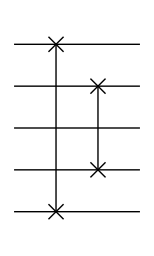
=-Graphics-

Figure 1. An implementation of quantum bit-reversal transform (QBR).

So far, we have done nothing but re-express the defining equation of the quantum Fourier transform. Now, we identify the elementary quantum logic gates that compose the transform. The product form in the above is remarkably simple to analyze. In particular, the state stored in the last qubit depends only on its own state y_n, and the relative phase factor ⅇ^(2π(ⅈ(0. y_n))_2) is equivalent to applying the Hadamard gate,

(0+1 ⅇ^(2π(ⅈ(0. y_n))_2))/(√2)=(0+(1(-1))^y_n)/(√2)=Hy_n .

The second last factor depends not only on the input state y_(n-1) of the second last qubit but also on the last qubit. However, the phase factor ⅇ^(2π(ⅈ(0. y_(n-1)))_2)governed by y_(n-1) is again equivalent to the Hadamard gate. On the other hand, the additional phase factor ⅇ^(2π(ⅈ(0.0 y_n))_2)=(ⅇ^(2π/2^2))^y_nis equivalent to operating the controlled-Z_2 gate, where

Z_k:=(1 | 0
0 | ⅇ^(2πⅈ/2^k)) ,

conditioned on the input state y_n of the last qubit. In short, the state stored in the second last qubit is given by

(0+1 ⅇ^(2π(ⅈ(0. y_(n-1)y_n))_2))/(√2)⊗y_n=(Z_2^y_n Hy_(n-1))⊗y_n .

More generally, the state on the k^th qubit

(0+1 ⅇ^(2π (ⅈ(0. y_k y_(k+1)(⋯y)_n))_2))/(√2)

is characterized by the relative phase angle

2(π(0. y_k y_(k+1)(…y)_n))_2=π y_k+(2π)/2^k(y_(k+1)(…y)_n)_2 .

The first part π y_k depends on the state y_k of the k^thqubit itself, and is equivalent to the relative phase angle resulting from the Hadamard gate,

Hy_k=(0+(1(-1))^y_k)/(√2).

The second part (2π)/2^k(y_(k+1)(…y)_n)_2  is governed by the qubits k+1, k+2, …, n through the integer (y_(k+1)(…y)_n)_2:=y_(k+1)2^k+…+y_(n-1)2^1+y_n associated with the bit string y_(k+1)(…y)_n. This corresponds to the controlled power of the phase gate Z_k. Putting it all together, we can regard that the above state  stored on the k^th qubit is a result of the transformation

y_k⊗y_(k+1)⊗⋯⊗y_n↦(Π_(j=1)^(k-1)Z_k^((y_(k+1)…y_n)_2)Hy_k)⊗y_(k+1)⊗⋯⊗y_n .

This is depicted by the quantum circuit in Figure 2.

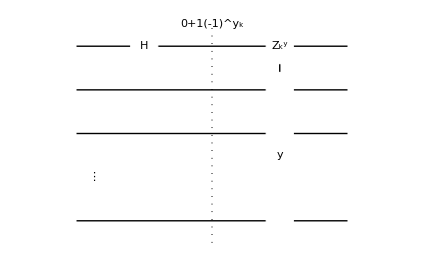

Figure 2. A quantum circuit illustrating the output state stored on the k^th qubit. Here, y is the integer with binary digits y_(k+1)y_(k+2)…y_n; that is, y:=(y_(k+1)y_(k+2)…y_n)_2.

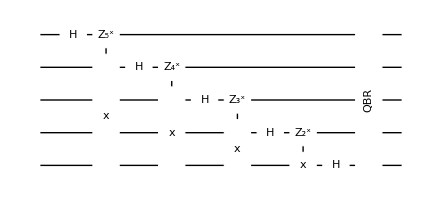

Figure 3. A quantum circuit for the quantum Fourier transform.

Overall, the quantum Fourier transform can be represented by the quantum circuit in Figure 3. By expanding each controlled-power gate in Figure 3 in a product of controlled-unitary gates, one can get an equivalent quantum circuit in Figure 4 for the quantum Fourier transform. This quantum circuit for the quantum Fourier transformation is found more commonly in the literature.

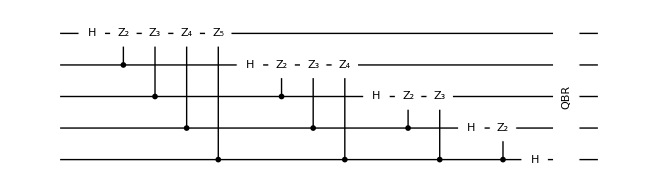

Figure 4. A quantum circuit for the quantum Fourier transform using elementary gates. Here, each of the controlled-power gates in Figure 3 is expanded in a product of controlled-unitary gates.

### Computational Complexity

From the quantum circuits discussed above, we see that quantum Fourier transform requires an order of n^2 elementary gates. For example, consider the quantum circuit in Figure 4. There are n Hadamard gates, one for each qubit. The number of controlled-unitary gates is given by ∑_(k=1)^n (k-1)=n(n-1)/2. There are n/2 SWAP gates as well, each of which requires three CNOT gates. Overall, we need n(n + 4)/2∼O(n^2) gates. This computational load is compared to O(n 2^n) gates for the fast Fourier transform (FFT), the best classical algorithm for the discrete Fourier transform.

### Demonstration

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Here, we simulate the quantum Fourier transform on a quantum register of 4 qubits.

```mathematica
$n=4;
```

Take a quantum register.

```mathematica
Let[Qubit,S]
SS=S[Range@$n,$]
```

{S_(,,1),S_(,,2),S_(,,3),S_(,,4)}

Define the QFT operator.

```mathematica
op=QFT[SS]
```

QFT[1,{S_(,,1),S_(,,2),S_(,,3),S_(,,4)},False]

For a reference, consider the quantum Fourier transform as a block unitary gate.

```mathematica
qc=QuantumCircuit[op]
```

-Graphics-

Now, construct the quantum circuit implementing the quantum Fourier transform.

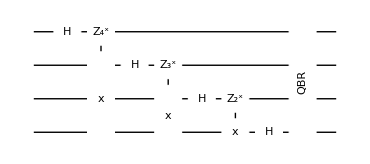

```mathematica
qc1a=Expand[op]
```

In the above quantum circuit, the label Z_k denotes the relative phase shift by 2π/2^k; that is, Z_k:=(1 | 0
0 | e^(2πⅈ/2^k)).

Further expand each of the controlled-power gate.

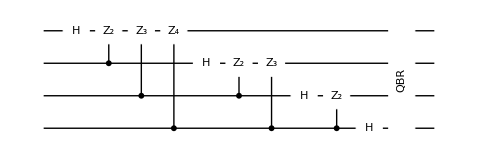

```mathematica
qc1b=ExpandAll[op]
```

To verify the above quantum circuit model, compare its matrix representation with the matrix for the discrete Fourier transform.

```mathematica
mat=Matrix[qc1a]//TrigToExp;
new=FourierMatrix[Power[2,$n]];
DeleteCases[new-mat//SimplifyThrough//Flatten,0]
```

{}

```mathematica
mat=Matrix[qc1b]//TrigToExp;
new=FourierMatrix[Power[2,$n]];
DeleteCases[new-mat//SimplifyThrough//Flatten,0]
```

{}

## Semiclassical Implementation

The semiclassical implementation is not only interesting from a physical point of view, but it is also extremely interesting given the current level of technology (Griffiths & Niu, 1996). Since it does not require any entanglement, a quantum information resource that is the most fragile and hence difficult to maintain, many experiments are using this implementation whenever the QFT and/or the quantum phase estimation is in need (Chiaverini, 2005; Higgins et al., 2007).

The line of argument in the original work (Griffiths & Niu, 1996) to derive the semiclassical implementation of the quantum Fourier transformation is interesting in its own right, and it offers another physically-motivated derivation of the quantum Fourier transform algorithm. Here, Instead, we simply make use of the relation between the quantum Fourier transform and its inverse.

The inverse quantum Fourier transform is given by

U_QFT^†X_y=1/2^(n/2)Σ_x X_x ⅇ^(-ⅈx p_y),

which follows directly from the orthogonality relation

1/2^n Σ_y ⅇ^(ⅈ(x-x')p_y)=δ_(x x').

This expression for the inverse quantum Fourier transform suggests that the inverse quantum Fourier transform is just another form of the quantum Fourier transform, and indeed, this is a characteristic property common to any kind of Fourier transform. This implies that one can recover the original quantum Fourier transform from the inverse quantum Fourier transform, and vice versa, in several ways.

For example, note that  U_QFT^†X_y is an element of the conjugate basis because

ⅇ^(-ⅈ x p_y)=ⅇ^(ⅈ x (2π-p_y))

for any x and y. In fact, U_QFT^†X_y=P_(2^n-y). More useful in the context of the semiclassical implementation of the quantum Fourier transform is to note that the inverse quantum Fourier transform U_QFT^† is nothing but the quantum Fourier transform with the phase factor ⅇ^(ⅈ x p_y) replaced by ⅇ^(-ⅈ x p_y). It corresponds to replacing the relative phase shifts Z_k in Figure 4 by Z_k^†. Conversely, if we start with the quantum circuit in Figure 4, take its Hermitian conjugate (i.e., inverse), and replace Z_k^† with Z_k, then we should recover the original quantum Fourier transform. Through this procedure, we get the quantum circuit in Figure 5 for the quantum Fourier transform.

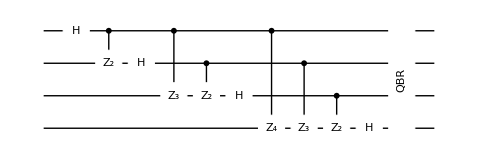

Figure 5. Another equivalent quantum circuit for quantum Fourier transform, where any Hadamard gate appears before the corresponding qubit k “controls” the phase shift Z_k on other qubits.

Compared to the quantum circuit in Figure 4, the above quantum circuit in Figure 5 has its Hadamard gate on a fixed qubit coming before the qubit “controls” the operation of the relative phase shift Z_k on other qubits. This difference brings a significant consequence. To make this clearer, we put measurements explicitly on the qubits as in Figure 6.

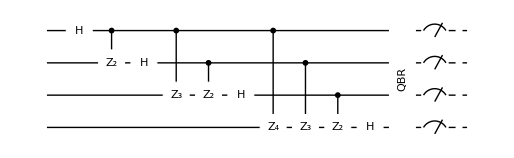

Figure 6. A quantum circuit equivalent to that in Figure 5, but with measurements displayed explicitly.

According to the principle of deferred measurement, the measurement can be performed before the controlled unitary gates as in Figure 7.

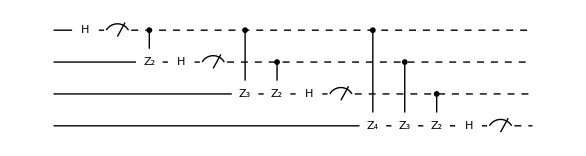

Figure 7. A quantum circuit to implement quantum Fourier transform semiclassically. Note that the classical bit string from measurement outcomes needs to be reversed.

This form is exactly the quantum circuit derived in Griffiths & Niu (1996). The important point is that after the measurement, the controlled-unitary gates become just classical feedback controls that require no entanglement.

### Demonstration

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Here, we simulate the semiclassical implementation of the quantum Fourier transform. Again, we consider a quantum register of four qubits.

```mathematica
$n=4;
SS=S[Range[$n],$];
```

Using the relation between the quantum Fourier transform and its inverse, one can construct another equivalent quantum circuit as follows. Here, the tilde accent emphasizes that the control qubits are in the reversed order.

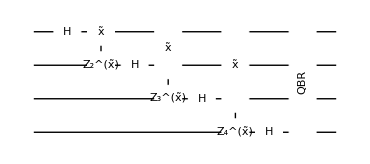

```mathematica
qc2a=Expand[op,"Reversed"]
```

Expand each of the controlled-power gates.

```mathematica
qc2b=ExpandAll[op,"Reversed"]
```

-Graphics-

Verify the above quantum circuit model by comparing its matrix representation with the matrix for the discrete Fourier transform.

```mathematica
mat=Matrix[qc2a]//TrigToExp;
new=FourierMatrix[Power[2,$n]];
DeleteCases[new-mat//SimplifyThrough//Flatten,0]
```

{}

```mathematica
mat=Matrix[qc2b]//TrigToExp;
new=FourierMatrix[Power[2,$n]];
DeleteCases[new-mat//SimplifyThrough//Flatten,0]
```

{}

Pick an input state randomly from the computational basis, and include the measurements as well.

```mathematica
in=Ket@@Thread[SS->RandomChoice[{0,1},$n]]
```

1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))

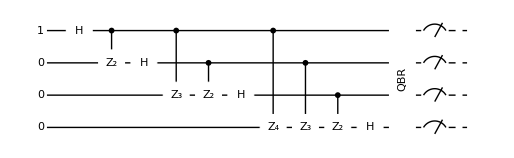

```mathematica
qc3=QuantumCircuit[in,qc2b,Measurement@Through[SS[3]]]
```

Convert the above quantum circuit to the form that is suitable for the semiclassical implementation of the quantum Fourier transform.

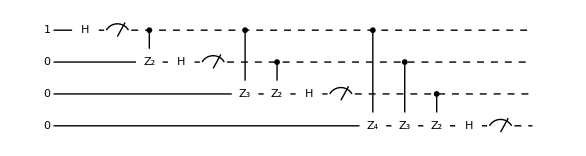

```mathematica
qc4=Drop[qc3,-2]/.{
S[k_,6]:>Sequence[S[k,6],Measurement[S[k,3]]]
}
```

To verify the equivalence of the two quantum circuit models, we compare the probability distributions.

```mathematica
EchoTiming[
data1=Table[Elaborate[qc3];FromDigits[Readout@Through[SS[3]],2],{500}];
]
```

44.1409

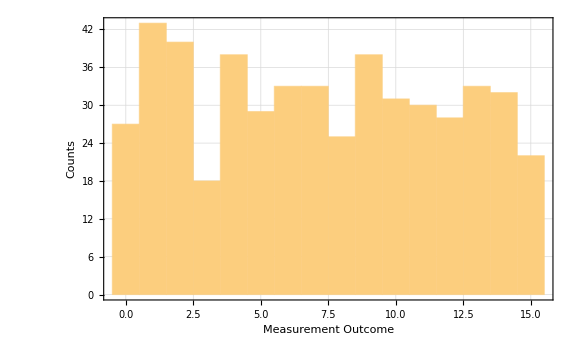

```mathematica
Histogram[data1,FrameLabel->{"Measurement Outcome","Counts"}]
```

Note that the bit strings of the measurement outcomes from the semiclassical model must be reversed .

```mathematica
EchoTiming[
data2=Table[ExpressionFor[qc4];FromDigits[Reverse@Readout@Through[SS[3]],2],{500}];
]
```

11.8478

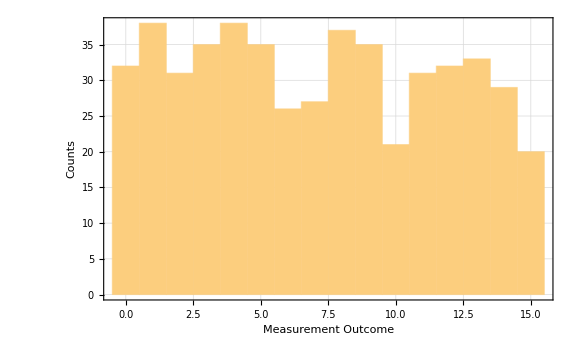

```mathematica
Histogram[data2,FrameLabel->{"Measurement Outcome","Counts"}]
```

The discrepancy between the two distributions is due to the finite sample size.

Another way to test the equivalence of the fully quantum and semiclassical implementation of the quantum Fourier transform is to randomly take an input state that ends up in a product state.

```mathematica
vecs=FourierMatrix[Power[2,$n],FourierParameters->{0,-1}].Basis[SS];
in=RandomChoice[vecs]
```

1/4 0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))+1/4 ⅇ^((3 ⅈ π)/4) 0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))-1/4 ⅈ 0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))+1/4 ⅇ^((ⅈ π)/4) 0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))-1/4 0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))+1/4 ⅇ^(-(ⅈ π)/4) 0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))+1/4 ⅈ 0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))+1/4 ⅇ^(-(3 ⅈ π)/4) 0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))+1/4 1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))+1/4 ⅇ^((3 ⅈ π)/4) 1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))-1/4 ⅈ 1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))+1/4 ⅇ^((ⅈ π)/4) 1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))-1/4 1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))0_(,,S_(,,4))+1/4 ⅇ^(-(ⅈ π)/4) 1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4))+1/4 ⅈ 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))+1/4 ⅇ^(-(3 ⅈ π)/4) 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))

```mathematica
qc=QuantumCircuit[ExpandAll[op,"Reversed"],Measurement[Through[SS[3]]]]
```

-Graphics-

```mathematica
qc1=QuantumCircuit[{in,"Label"->"in"},qc,"PortSize"->{1.2,0.5}]
```

-Graphics-

```mathematica
qc2=qc1/.{_Measurement->Nothing,_Swap->Nothing}/.{
S[k_,6]:>Sequence[S[k,6],Measurement[S[k,3]]]
}
```

-Graphics-

```mathematica
out1=ExpressionFor[qc1]
```

1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))

Again, recall that the order of qubits are reversed in the semiclassical implementation.

```mathematica
out2=ExpressionFor[qc2]//Chop
```

1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))

| Related Guides
▪Quantum Information Systems
▪Q3

| Related Tech Notes
▪Quantum Fourier Transform: Semiclassical Implementation
▪Quantum Phase Estimation
▪Quantum Algorithms
▪QuantumCircuit Usage Examples
▪Quantum Information Systems with Q3
▪Quick Quantum Computing with Q3

| Related Links
▪A. Y. Kitaev, Electronic Colloquium on Computational Complexity 3, 3 (1996)http://arxiv.org/abs/quant-ph/9511026, “Quantum Measurements and the Abelian Stabilizer Problem.”
▪R. B. Griffiths and C.-S. Niu, Physical Review Letters 76 (17), 3228 (1996)https://doi.org/10.1103/physrevlett.76.3228, “Semiclassical Fourier Transform for Quantum Computation.”
▪J. Chiaverini https://doi.org/10.1126%2Fscience.1110335et al., Science 308 (5724), 997 (2005)https://doi.org/10.1126%2Fscience.1110335, “Implementation of the Semiclassical Quantum Fourier Transform in a Scalable System.”
▪B. L. Higgins, D. W. Berry, S. D. Bartlett, H. M. Wiseman, & G. J. Pryde, Nature 450 (7168), 393 (2007)https://doi.org/10.1038/nature06257, “Entanglement-free Heisenberg-limited phase estimation.”
▪Hermann Weyl (1931)https://www.google.com/books/edition/_/jQbEcDDqGb8C?hl=en, The theory of groups and quantum mechanics (Dover, 1931).
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).